```mathematica
g[N_]:=Tally[Fl
atten[Table[Table[Table[i^2+k^2+j^2,{i,0,N}],{j,0,N}],{k,0,N}],3]]
```

```mathematica
a=Sort[g[150]];
```

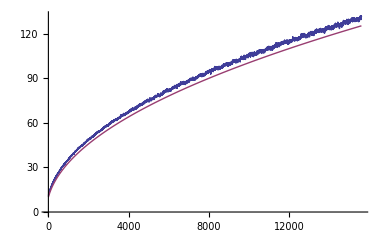

```mathematica
ListPlot[{b,Table[{i,Sqrt[i+n/2]},{i,0,Length[a]/3}]},Joined->True]
```

```mathematica
n=200;b={};For[i=1,i<Length[a]/3,i++,
AppendTo[b,1/n(Sum[a[[i+k,2]],{k,0,n-1}])];]
```

$Aborted